### Categorization

Tutorial

MaTeX

MaTeX`

MaTeX/tutorial/PreparingFiguresToSize

### Keywords

figures

publication figure

font size

graphics export

Details

# Preparing Figures to Size

This is a tutorial on preparing high-quality publication figures which have easily readable labels and fit well with the style of the surrounding document. MaTeX is not needed to achieve this. However, this is a task that most MaTeX users will face.

While the examples in this tutorial show how to include figures in a LATEX document, the same principles apply to any other document preparation system, such as Microsoft Word.

## Why prepare to size?

A good figure is made to a given physical size, and should not be arbitrarily re-scaled when including it in a document. This way we can control the text size in the figure precisely. We can make sure that it is big enough to be readable and that it matches the surrounding text, as well as the text in other figures. Deciding on a physical size also makes it straightforward to choose an appropriate resolution for rasterized figure elements (such as Mathematica's 3D graphics).

Thus, do not specify the size when including the figure in LATEX, as that triggers rescaling. Do not do this:

\includegraphics[width=8cm]{myfig}

Instead, specify the size only when creating the figure in Mathematica. When exporting it, the size will be encoded into the PDF or EPS output, so LATEX will know how to size it correctly. Simply use:

\includegraphics{myfig}

## Basic unit types

You may have noticed that when re-sizing a typical Mathematica figure, the size of text does not change:

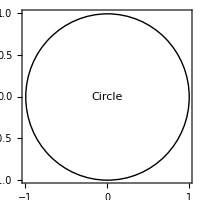
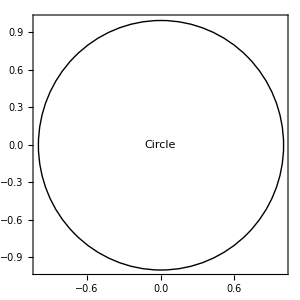

```mathematica
Graphics[{Circle[],FontSize->20,Text["Circle"]},Frame->True,ImageSize->#]&/@{200,300}
```

This is because font sizes are interpreted in absolute physical units (printer's points), which are independent of the image size.

The key to effectively controlling the relative sizes of various figure elements is understanding Mathematica's three different types of units. These are:

Plot coordinates, which line up with the coordinate system. Objects given in plot coordinates scale with the figure (i.e. ImageSize), and their size is affected by PlotRange.

Scaled coordinates, which run from 0 to 1 across the plot range, and thus also scale with the image size. (There is also the rarely used ImageScaled, which assumes coordinates to run from 0 to 1 across the whole figure, including margins, and not just the plot range.)

Absolute coordinates, which are given in printer's points and do not scale with the image size. They can be specified using Offset.

Let us look at some examples. We can give font sizes in Scaled units to force the text to scale with the image:

```mathematica
Graphics[{Circle[],FontSize->Scaled[0.1], Text["Circle"]}, Frame -> True, ImageSize -> #] & /@ {200, 300}
```

{-Graphics-,-Graphics-}

Mathematica always assumes a screen resolution of 72 dpi. Since 1 inch is equal to 72 points, absolute coordinates are equivalent to pixels when displayed on a screen. When exporting to vector formats such as PDF or EPS, they are interpreted as PostScript points.

Different Graphics options and directives assume different types of units by default. For example, PlotRangePadding is interpreted in plot coordinates, PointSize uses scaled coordinates, and ImageSize, ImagePadding or AbsolutePointSize are assumed to be in absolute coordinates. In some options, the coordinate type can be changed to scaled by wrapping the values with the Scaled head.

Equipped with this knowledge, now we can create figures which have graphics elements with different scaling behaviours. The following figure contains a Rectangle given in Scaled coordinates, which serves as a light green background within the plot frame; a Circle of radius 2, in plot coordinates; and some text with a Polygon hat of matching size over it, in absolute coordinates.

```mathematica
fig=Graphics[{
{RGBColor[0.7,0.9,0.7],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},
Circle[{0,0},2],
Text[
Style["hello",FontSize->16,FontFamily->"Helvetica"],
{0,0}
],
Polygon[{
Offset[{-19,11},{0,0}],
Offset[{19,11},{0,0}],
Offset[{0,15},{0,0}]
}]
},
Frame->True,
PlotRangePadding->0.2
]
```

-Graphics-

Try resizing this figure with the mouse and see how the different elements scale. The background rectangle and the circle scale with the frame, while the text and the polygon remain at the same pixel size (or size in points, if exporting to printable formats).

```mathematica
Show[fig,ImageSize->360]
```

-Graphics-

Changing the plot range only affects properties which are given in plot coordinates: the size and location of the circle, and the location of the text. The size of the text (and its hat) stays constant.

```mathematica
Show[fig,PlotRange->{{-3,4},{-3,4}}]
```

-Graphics-

## Exporting figures to size

When exporting to the PDF or EPS formats, the value of the ImageSize option is interpreted in PostScript points. It is more convenient to use familiar units like centimetres or inches. Thus we define

```mathematica
inch=72; (* 72 points in an inch *)
cm=72/2.54; (* 1 inch = 2.54 cm *)
```

Then to create a 10 cm wide PDF figure, we can use

```mathematica
Export["figure.pdf",Show[fig,ImageSize->10cm],"PDF"]
```

Since text size does not scale with the image, it is important to preview the result directly in the notebook. This can be done by setting the ImageSize option directly:

-Graphics-

The problem with this is that Mathematica assumes 1 point = 1 pixel, regardless of the actual resolution of the screen. On modern screens this results in the figures being displayed at an inconveniently small size. For example, a 6 cm wide figure with 8 pt fonts looks like this:

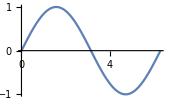

```mathematica
Plot[Sin[x],{x,0,2Pi},BaseStyle->{FontSize->8},ImageSize->6cm]
```

It is more convenient to look at a magnified version of the same:

```mathematica
fig=Plot[Sin[x],{x,0,2Pi},BaseStyle->{FontSize->8},ImageSize->6cm];
Magnify[fig,1.5]
```

-Graphics-

## Example workflow

For this example, let us create a two-column REVTeX document, and include both a single-column and a wide figure. The default REVTeX text- and column-widths are 510 pt and 246 pt (see the source document below on how to measure them).

We will use the default 10 pt font size for the main text. Then the figure captions will be 9 pt in size—let us use this size in figure labels as well. It is convenient to set the font size permanently for the plotting functions that we are going to use, including MaTeX:

```mathematica
<<MaTeX`
```

```mathematica
fontSize=9;
SetOptions[MaTeX,FontSize->fontSize];
SetOptions[Plot,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Math"}];
```

Due to a quirk in how Mathematica handles plot legends, we must set one additional option to avoid shrinking legended plots at the time of export:

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

Warning: This setting will maintain its effect until Mathematica is fully restarted.

Let us now create the two figures, and export them to PDF. Note that the ImageSize option is explicitly set on each plot.

Note: The cells containing the export commands are disabled below, to prevent accidentally overwriting files when evaluating this notebook. To evaluate them, copy and paste the commands into a new cell.

```mathematica
fig=Plot[{Tan[x],Sec[x]},{x,0,2Pi},
Ticks->{Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,0,2Pi,Pi/4}],Automatic},
PlotLegends->Placed[MaTeX[{Tan[x],Sec[x]}],{Bottom,Center}],
AxesStyle->BlackFrame,
ImageSize->246 (* one-column figure width *)
]
```

-Graphics-

```mathematica
Export["fig1.pdf",fig]
```

Evaluating the following example requires Mathematica 11.0 or later due to the use of Callout:

```mathematica
fig=Plot[
Evaluate@MapThread[
Callout[#1,MaTeX[#1],#2,LeaderSize->{1}]&,
{{Sin[x],Cos[x]},{Above,Below}}
],
{x,-2Pi,2Pi},
Ticks->{
Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,-2Pi,2Pi,Pi/4}],
Automatic
},
AxesStyle->BlackFrame,
AspectRatio->1/3,
PlotRangePadding->{0.5,1},
ImageSize->510 (* two-column figure width *)
]
```

-Graphics-

```mathematica
Export["fig2.pdf",fig]
```

The full source of the LATEX document is below:

\documentclass[twocolumn,letterpaper,10pt]{revtex4-1}

\usepackage{graphicx}
\usepackage{lipsum} % package for filler text

\begin{document}

\title{Sample Manuscript}

\begin{abstract}
This short sample document illustrates embedding figures that were prepared to a certain physical size and have fonts that are consistent with the rest of the document in size and style.
\end{abstract}

\maketitle

% determine column and text widths as below:
\emph{The full text width in this document is \the\textwidth, while the column width is \the\columnwidth.  We will use these values to prepare the figures in Mathematica.}

\lipsum[1-2] % placeholder text

\begin{figure}[b]
\includegraphics{fig1} % do not set width!
\caption{Tangent and secant functions.}
\end{figure}

\begin{figure*}
\includegraphics{fig2} % do not set width!
\caption{Sine and cosine functions.}
\end{figure*}

\lipsum[3-10] % placeholder text

\end{document}

After compiling with pdflatex, the document will look like this:

-Graphics-

More About

Related Tutorials

Typesetting with MaTeX

Related Wolfram Education Group Courses